# Pango analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/pango-countries

## Setup

### Parameters

```mathematica
dataset="pango-countries";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=300;
```

```mathematica
gridCount=1;
```

```mathematica
rtMax=1.8;
```

```mathematica
rtMin=0.6;
```

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01","2022-03-01","2022-04-01","2022-05-01","2022-06-01","2022-07-01","2022-08-01","2022-09-01","2022-10-01","2022-11-01","2022-12-01"};
```

### Countries

```mathematica
countriesToDrop={};
```

## Variants and colors

### Import

```mathematica
variantData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=variantData[[1]]
```

{date,location,variant,median_R,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,R_upper_95→5,R_lower_95→6,R_upper_80→7,R_lower_80→8,R_upper_50→9,R_lower_50→10,median_freq→11}

```mathematica
variantData=Drop[variantData,1];
```

```mathematica
variants=Union[variantData[[All,3]]]
```

{BA.2,BA.2.3.20,BA.2.75,BA.2.75.2,BA.2.75.4,BA.4.6,BA.5,BA.5.1,BA.5.1.10,BA.5.1.18,BA.5.1.27,BA.5.1.5,BA.5.1.6,BA.5.2,BA.5.2.1,BA.5.2.16,BA.5.2.20,BA.5.2.21,BA.5.2.23,BA.5.2.34,BA.5.2.35,BA.5.2.6,BA.5.2.9,BA.5.3,BA.5.5,BA.5.6,BE.1,BE.1.1,BE.1.1.1,BE.1.2.1,BE.1.4,BE.4.2,BF.10,BF.11,BF.13,BF.14,BF.26,BF.5,BF.7,BF.7.4,BF.7.4.1,BF.7.5,BN.1,BN.1.2,BN.1.3,BN.1.3.1,BN.1.4,BN.1.5,BQ.1,BQ.1.1,BQ.1.10,BQ.1.10.1,BQ.1.1.1,BQ.1.11,BQ.1.1.13,BQ.1.1.18,BQ.1.12,BQ.1.1.28,BQ.1.1.3,BQ.1.13,BQ.1.1.4,BQ.1.14,BQ.1.1.5,BQ.1.15,BQ.1.1.6,BQ.1.1.7,BQ.1.18,BQ.1.2,BQ.1.22,BQ.1.23,BQ.1.25,BQ.1.3,BQ.1.5,BQ.1.6,BQ.1.8,CH.1.1,CK.1,CQ.2,CR.1.1,DF.1,other,XBB,XBB.1,XBB.1.5,XBB.2,XBB.3}

```mathematica
n=Length[variants]
```

86

### Max frequency

```mathematica
variantFrequencyMapping=Table[variant->Max[Cases[variantData,x_/;x[[3]]==variant][[All,11]]],{variant,variants}];
```

```mathematica
highFrequencyVariants=Cases[variantFrequencyMapping,x_/;x[[2]]>=0.005][[All,1]];
```

```mathematica
Length[highFrequencyVariants]
```

58

```mathematica
lowFrequencyVariants=Complement[variants,highFrequencyVariants];
```

```mathematica
Length[lowFrequencyVariants]
```

28

```mathematica
variants=Join[highFrequencyVariants,lowFrequencyVariants];
```

```mathematica
n=Length[variants]
```

86

### Variant to clade mapping and clade colors

```mathematica
toHexString[n_Integer]:=StringJoin[ToString/@(IntegerDigits[n,16]/.Thread[Range[10,15]->CharacterRange["A","F"]])]
```

```mathematica
rgbColorToHex[rgbColor_]:="#"<>StringJoin[Map[toHexString[Round[#*255]]&,Level[rgbColor,1]]]
```

```mathematica
start[n_]:=0.05;
```

```mathematica
stop[n_]:=0.99;
```

```mathematica
gap[n_]:=(stop[n]-start[n])/(n-1)
```

```mathematica
makeColors[n_]:=Table[ColorData["Rainbow"][i],{i,start[n],stop[n],gap[n]}];
```

```mathematica
startGrays[n_]:=0.35;
```

```mathematica
stopGrays[n_]:=0.65;
```

```mathematica
gapGrays[n_]:=(stopGrays[n]-startGrays[n])/(n-1)
```

```mathematica
makeGrays[n_]:=Table[GrayLevel[i],{i,startGrays[n],stopGrays[n],gapGrays[n]}];
```

```mathematica
variantToClade=Map[#[[1]]->#[[2]]&,Drop[Import["../../data/pango-countries/pango_aliasing.tsv"],1]];
```

```mathematica
clades={"other","21L (Omicron)","22A (Omicron)","22B (Omicron)","22C (Omicron)","22D (Omicron)","22E (Omicron)","22F (Omicron)"};
```

```mathematica
cladeColors=Prepend[makeColors[Length[clades]-1],Gray]
```

{GrayLevel[0.5],RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],RGBColor[0.54357188, 0.73433536, 0.41441192],RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],RGBColor[0.86067868, 0.15704232000000004, 0.13666448]}

```mathematica
cladeToColor=MapThread[#1->#2&,{clades,cladeColors}]
```

{other→GrayLevel[0.5],21L (Omicron)→RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],22A (Omicron)→RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],22B (Omicron)→RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],22C (Omicron)→RGBColor[0.54357188, 0.73433536, 0.41441192],22D (Omicron)→RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],22E (Omicron)→RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],22F (Omicron)→RGBColor[0.86067868, 0.15704232000000004, 0.13666448]}

### Colors

```mathematica
colorMappingForClade[clade_]:=Module[{pos,shades,tints,col},
pos=Flatten[Position[variants,x_/;(x/.variantToClade)==clade]];
If[Length[pos]>0,
shades=Reverse[Table[Darker[clade/.cladeToColor,x],{x,0,0.5,1/(Length[pos])}]];
tints=Drop[Table[Lighter[clade/.cladeToColor,x],{x,0,0.5,1/(Length[pos])}],1];
col=Join[shades,tints];
Table[variants[[pos[[i]]]]->col[[i]],{i,Length[pos]}],
{}
]
]
```

```mathematica
variantColorMapping=Flatten[Map[colorMappingForClade,clades]]
```

{other→RGBColor[0.5, 0.5, 0.5],BA.2→RGBColor[0.1715652, 0.057908600000000005, 0.31848920000000003],BA.2.3.20→RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],BA.4.6→RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],BA.5→RGBColor[0.17514764, 0.3213289933333333, 0.3316169066666667],BA.5.1→RGBColor[0.183905022, 0.337395443, 0.3481977520000001],BA.5.1.10→RGBColor[0.19266240399999998, 0.3534618926666666, 0.3647785973333334],BA.5.1.18→RGBColor[0.201419786, 0.3695283423333333, 0.3813594426666667],BA.5.1.27→RGBColor[0.210177168, 0.38559479199999996, 0.39794028800000003],BA.5.1.5→RGBColor[0.21893455, 0.4016612416666666, 0.4145211333333334],BA.5.2→RGBColor[0.22769193199999999, 0.4177276913333333, 0.4311019786666668],BA.5.2.1→RGBColor[0.236449314, 0.43379414099999997, 0.44768282400000003],BA.5.2.20→RGBColor[0.245206696, 0.4498605906666666, 0.4642636693333334],BA.5.2.21→RGBColor[0.253964078, 0.4659270403333333, 0.4808445146666667],BA.5.2.23→RGBColor[0.26272145999999996, 0.48199348999999997, 0.49742536000000004],BA.5.2.34→RGBColor[0.271478842, 0.4980599396666666, 0.5140062053333334],BA.5.2.6→RGBColor[0.280236224, 0.5141263893333333, 0.5305870506666668],BA.5.2.9→RGBColor[0.288993606, 0.5301928389999999, 0.547167896],BA.5.3→RGBColor[0.297750988, 0.5462592886666666, 0.5637487413333334],BA.5.5→RGBColor[0.30650837, 0.5623257383333333, 0.5803295866666668],BA.5.6→RGBColor[0.315265752, 0.5783921879999999, 0.596910432],BE.1→RGBColor[0.324023134, 0.5944586376666666, 0.6134912773333334],BE.1.1→RGBColor[0.33278051599999997, 0.6105250873333333, 0.6300721226666668],BF.10→RGBColor[0.341537898, 0.6265915369999999, 0.646652968],BF.11→RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],BF.13→RGBColor[0.366537898, 0.6515915369999999, 0.6716529680000001],BF.26→RGBColor[0.38278051599999996, 0.6605250873333333, 0.6800721226666667],BF.5→RGBColor[0.399023134, 0.6694586376666666, 0.6884912773333334],BF.7→RGBColor[0.415265752, 0.678392188, 0.6969104320000001],BF.7.4→RGBColor[0.43150837, 0.6873257383333333, 0.7053295866666668],BF.7.4.1→RGBColor[0.447750988, 0.6962592886666666, 0.7137487413333334],CK.1→RGBColor[0.46399360599999995, 0.705192839, 0.7221678960000001],CQ.2→RGBColor[0.480236224, 0.7141263893333333, 0.7305870506666667],BA.5.1.6→RGBColor[0.49647884200000003, 0.7230599396666666, 0.7390062053333334],BA.5.2.16→RGBColor[0.51272146, 0.73199349, 0.74742536],BA.5.2.35→RGBColor[0.528964078, 0.7409270403333333, 0.7558445146666668],BE.1.1.1→RGBColor[0.5452066959999999, 0.7498605906666667, 0.7642636693333333],BE.1.2.1→RGBColor[0.561449314, 0.758794141, 0.7726828240000001],BE.1.4→RGBColor[0.577691932, 0.7677276913333333, 0.7811019786666668],BE.4.2→RGBColor[0.59393455, 0.7766612416666666, 0.7895211333333334],BF.14→RGBColor[0.610177168, 0.7855947919999999, 0.797940288],BF.7.5→RGBColor[0.626419786, 0.7945283423333334, 0.8063594426666667],CR.1.1→RGBColor[0.642662404, 0.8034618926666667, 0.8147785973333334],DF.1→RGBColor[0.6589050219999999, 0.812395443, 0.823197752],BA.2.75→RGBColor[0.38951687999999995, 0.36243652666666665, 0.13373712666666668],BN.1→RGBColor[0.4674202559999999, 0.43492383199999995, 0.160484552],BN.1.3→RGBColor[0.5453236319999999, 0.5074111373333333, 0.18723197733333335],CH.1.1→RGBColor[0.623227008, 0.5798984426666667, 0.21397940266666668],BA.2.75.2→RGBColor[0.7011303839999999, 0.6523857479999999, 0.240726828],BA.2.75.4→RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],BN.1.2→RGBColor[0.8011303839999999, 0.752385748, 0.34072682800000004],BN.1.3.1→RGBColor[0.8232270079999999, 0.7798984426666666, 0.41397940266666666],BN.1.4→RGBColor[0.8453236319999999, 0.8074111373333333, 0.48723197733333334],BN.1.5→RGBColor[0.867420256, 0.834923832, 0.560484552],BQ.1→RGBColor[0.4508135, 0.26993600000000006, 0.10418300000000001],BQ.1.1→RGBColor[0.4854914615384615, 0.29070030769230776, 0.11219707692307693],BQ.1.10→RGBColor[0.520169423076923, 0.31146461538461545, 0.12021115384615386],BQ.1.11→RGBColor[0.5548473846153845, 0.33222892307692314, 0.12822523076923079],BQ.1.1.18→RGBColor[0.5895253461538461, 0.35299323076923084, 0.13623930769230772],BQ.1.12→RGBColor[0.6242033076923077, 0.37375753846153853, 0.14425338461538462],BQ.1.1.3→RGBColor[0.6588812692307692, 0.3945218461538462, 0.15226746153846155],BQ.1.13→RGBColor[0.6935592307692308, 0.41528615384615397, 0.16028153846153848],BQ.1.1.4→RGBColor[0.7282371923076922, 0.4360504615384616, 0.1682956153846154],BQ.1.14→RGBColor[0.7629151538461538, 0.45681476923076936, 0.17630969230769233],BQ.1.1.5→RGBColor[0.7975931153846153, 0.47757907692307705, 0.18432376923076926],BQ.1.2→RGBColor[0.8322710769230769, 0.49834338461538474, 0.19233784615384616],BQ.1.22→RGBColor[0.8669490384615384, 0.5191076923076924, 0.2003519230769231],BQ.1.23→RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],BQ.1.25→RGBColor[0.9054105769230769, 0.5575692307692309, 0.23881346153846156],BQ.1.3→RGBColor[0.9091941538461538, 0.5752664615384616, 0.2692609230769231],BQ.1.5→RGBColor[0.9129777307692307, 0.5929636923076924, 0.2997083846153846],BQ.1.10.1→RGBColor[0.9167613076923077, 0.6106609230769232, 0.3301558461538462],BQ.1.1.1→RGBColor[0.9205448846153845, 0.628358153846154, 0.36060330769230775],BQ.1.1.13→RGBColor[0.9243284615384615, 0.6460553846153847, 0.39105076923076926],BQ.1.15→RGBColor[0.9281120384615384, 0.6637526153846155, 0.42149823076923076],BQ.1.1.6→RGBColor[0.9318956153846154, 0.6814498461538463, 0.4519456923076923],BQ.1.1.7→RGBColor[0.9356791923076923, 0.699147076923077, 0.4823931538461539],BQ.1.18→RGBColor[0.9394627692307692, 0.7168443076923078, 0.5128406153846155],BQ.1.6→RGBColor[0.9432463461538462, 0.7345415384615386, 0.5432880769230769],BQ.1.8→RGBColor[0.947029923076923, 0.7522387692307693, 0.5737355384615385],XBB→RGBColor[0.516407208, 0.09422539200000002, 0.081998688],XBB.1→RGBColor[0.688542944, 0.12563385600000004, 0.10933158400000001],XBB.1.5→RGBColor[0.86067868, 0.15704232000000004, 0.13666448],XBB.2→RGBColor[0.888542944, 0.32563385600000005, 0.30933158400000005],XBB.3→RGBColor[0.916407208, 0.49422539200000004, 0.481998688]}

```mathematica
highFrequencyColors=highFrequencyVariants/.variantColorMapping
```

{RGBColor[0.1715652, 0.057908600000000005, 0.31848920000000003],RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.38951687999999995, 0.36243652666666665, 0.13373712666666668],RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],RGBColor[0.17514764, 0.3213289933333333, 0.3316169066666667],RGBColor[0.183905022, 0.337395443, 0.3481977520000001],RGBColor[0.19266240399999998, 0.3534618926666666, 0.3647785973333334],RGBColor[0.201419786, 0.3695283423333333, 0.3813594426666667],RGBColor[0.210177168, 0.38559479199999996, 0.39794028800000003],RGBColor[0.21893455, 0.4016612416666666, 0.4145211333333334],RGBColor[0.22769193199999999, 0.4177276913333333, 0.4311019786666668],RGBColor[0.236449314, 0.43379414099999997, 0.44768282400000003],RGBColor[0.245206696, 0.4498605906666666, 0.4642636693333334],RGBColor[0.253964078, 0.4659270403333333, 0.4808445146666667],RGBColor[0.26272145999999996, 0.48199348999999997, 0.49742536000000004],RGBColor[0.271478842, 0.4980599396666666, 0.5140062053333334],RGBColor[0.280236224, 0.5141263893333333, 0.5305870506666668],RGBColor[0.288993606, 0.5301928389999999, 0.547167896],RGBColor[0.297750988, 0.5462592886666666, 0.5637487413333334],RGBColor[0.30650837, 0.5623257383333333, 0.5803295866666668],RGBColor[0.315265752, 0.5783921879999999, 0.596910432],RGBColor[0.324023134, 0.5944586376666666, 0.6134912773333334],RGBColor[0.33278051599999997, 0.6105250873333333, 0.6300721226666668],RGBColor[0.341537898, 0.6265915369999999, 0.646652968],RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],RGBColor[0.366537898, 0.6515915369999999, 0.6716529680000001],RGBColor[0.38278051599999996, 0.6605250873333333, 0.6800721226666667],RGBColor[0.399023134, 0.6694586376666666, 0.6884912773333334],RGBColor[0.415265752, 0.678392188, 0.6969104320000001],RGBColor[0.43150837, 0.6873257383333333, 0.7053295866666668],RGBColor[0.447750988, 0.6962592886666666, 0.7137487413333334],RGBColor[0.4674202559999999, 0.43492383199999995, 0.160484552],RGBColor[0.5453236319999999, 0.5074111373333333, 0.18723197733333335],RGBColor[0.4508135, 0.26993600000000006, 0.10418300000000001],RGBColor[0.4854914615384615, 0.29070030769230776, 0.11219707692307693],RGBColor[0.520169423076923, 0.31146461538461545, 0.12021115384615386],RGBColor[0.5548473846153845, 0.33222892307692314, 0.12822523076923079],RGBColor[0.5895253461538461, 0.35299323076923084, 0.13623930769230772],RGBColor[0.6242033076923077, 0.37375753846153853, 0.14425338461538462],RGBColor[0.6588812692307692, 0.3945218461538462, 0.15226746153846155],RGBColor[0.6935592307692308, 0.41528615384615397, 0.16028153846153848],RGBColor[0.7282371923076922, 0.4360504615384616, 0.1682956153846154],RGBColor[0.7629151538461538, 0.45681476923076936, 0.17630969230769233],RGBColor[0.7975931153846153, 0.47757907692307705, 0.18432376923076926],RGBColor[0.8322710769230769, 0.49834338461538474, 0.19233784615384616],RGBColor[0.8669490384615384, 0.5191076923076924, 0.2003519230769231],RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],RGBColor[0.9054105769230769, 0.5575692307692309, 0.23881346153846156],RGBColor[0.9091941538461538, 0.5752664615384616, 0.2692609230769231],RGBColor[0.9129777307692307, 0.5929636923076924, 0.2997083846153846],RGBColor[0.623227008, 0.5798984426666667, 0.21397940266666668],RGBColor[0.46399360599999995, 0.705192839, 0.7221678960000001],RGBColor[0.480236224, 0.7141263893333333, 0.7305870506666667],RGBColor[0.5, 0.5, 0.5],RGBColor[0.516407208, 0.09422539200000002, 0.081998688],RGBColor[0.688542944, 0.12563385600000004, 0.10933158400000001],RGBColor[0.86067868, 0.15704232000000004, 0.13666448],RGBColor[0.888542944, 0.32563385600000005, 0.30933158400000005]}

```mathematica
lowFrequencyColors=makeGrays[Length[lowFrequencyVariants]]
```

{GrayLevel[0.35],GrayLevel[0.3611111111111111],GrayLevel[0.3722222222222222],GrayLevel[0.3833333333333333],GrayLevel[0.39444444444444443],GrayLevel[0.40555555555555556],GrayLevel[0.41666666666666663],GrayLevel[0.42777777777777776],GrayLevel[0.4388888888888889],GrayLevel[0.44999999999999996],GrayLevel[0.4611111111111111],GrayLevel[0.4722222222222222],GrayLevel[0.4833333333333333],GrayLevel[0.49444444444444446],GrayLevel[0.5055555555555555],GrayLevel[0.5166666666666666],GrayLevel[0.5277777777777778],GrayLevel[0.5388888888888889],GrayLevel[0.55],GrayLevel[0.5611111111111111],GrayLevel[0.5722222222222222],GrayLevel[0.5833333333333333],GrayLevel[0.5944444444444444],GrayLevel[0.6055555555555556],GrayLevel[0.6166666666666667],GrayLevel[0.6277777777777778],GrayLevel[0.6388888888888888],GrayLevel[0.6499999999999999]}

```mathematica
colors=Join[highFrequencyColors,lowFrequencyColors];
```

```mathematica
legendPanel=PointLegend[highFrequencyColors,highFrequencyVariants,LabelStyle->Directive[FontSize->10],LegendMarkerSize->20,LegendLayout->{"Column",7},Spacings->{0,0.1}]
```

```mathematica
variantToColor=MapThread[#1->#2&,{variants,colors}];
```

```mathematica
variantToIndex=MapThread[#1->#2&,{variants,Range[n]}];
```

## Rt estimates

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,R_upper_95→5,R_lower_95→6,R_upper_80→7,R_lower_80→8,R_upper_50→9,R_lower_50→10,median_freq→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
startDate=DateString[DatePlus[First[Sort[rtData[[All,1]]]],10],{"Year","-","Month", "-","Day"}]
```

2022-09-01

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2022-12-19

```mathematica
endDate=Last[Sort[rtData[[All,1]]]]
```

2022-12-19

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countries=Union[rtData[[All,2]]]
```

{USA}

```mathematica
countries=DeleteCases[countries,x_/;MemberQ[countriesToDrop,x]]
```

{USA}

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[11]]>0.005];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{rtMin,rtMax}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

```mathematica
rtPanels=Map[countryRtPlot,countries];
```

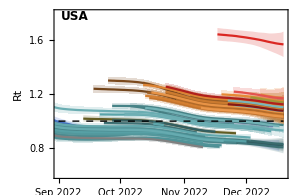
-Graphics- |

```mathematica
fig=Grid[{{countryRtPlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt.png

```mathematica
finalRts=Table[If[Length[rtGather["USA",variant]]>0,rtGather["USA",variant][[-1,2]],Null],{variant,variants}];
```

```mathematica
finalRtsLower=Table[If[Length[rtGatherLower["USA",variant]]>0,rtGatherLower["USA",variant][[-1,2]],Null],{variant,variants}];
```

```mathematica
finalRtsUpper=Table[If[Length[rtGatherUpper["USA",variant]]>0,rtGatherUpper["USA",variant][[-1,2]],Null],{variant,variants}];
```

## Prevalence

```mathematica
pData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I_smooth,I_smooth_upper_95,I_smooth_lower_95,I_smooth_upper_80,I_smooth_lower_80,I_smooth_upper_50,I_smooth_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I_smooth→4,I_smooth_upper_95→5,I_smooth_lower_95→6,I_smooth_upper_80→7,I_smooth_lower_80→8,I_smooth_upper_50→9,I_smooth_lower_50→10,median_freq→11}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{200,100000}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,20,100,200,1000,2000,10000,20000,100000,200000,1000000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

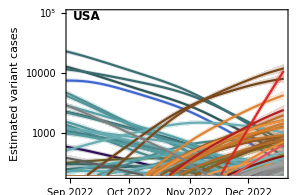
-Graphics- |

```mathematica
fig=Grid[{{countryPrevalencePlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-log-cases.png

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,32000}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

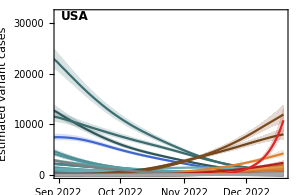
-Graphics- |

```mathematica
fig=Grid[{{countryPrevalencePlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-cases.png

## Frequency

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
fData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_freq-combined-"<>model<>".tsv"];
```

```mathematica
header=fData[[1]]
```

{date,location,variant,median_freq,freq_upper_95,freq_lower_95,freq_upper_80,freq_lower_80,freq_upper_50,freq_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_freq→4,freq_upper_95→5,freq_lower_95→6,freq_upper_80→7,freq_lower_80→8,freq_upper_50→9,freq_lower_50→10}

```mathematica
fData=Drop[fData,1];
```

```mathematica
fGather[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
fGatherLower[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
fGatherUpper[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
logitTransformDateSeries[dateSeries_]:=Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,dateSeries]
```

```mathematica
variantCountryFrequencyPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=logitTransformDateSeries[fGather[country,variant]];
lowerSeries=logitTransformDateSeries[fGatherLower[country,variant]];
upperSeries=logitTransformDateSeries[fGatherUpper[country,variant]];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant frequency"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{logitTransform[0.0005],logitTransform[0.9]}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryFrequencyPlot[country_]:=Show[Table[variantCountryFrequencyPlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

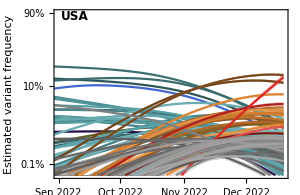
-Graphics- |

```mathematica
fig=Grid[{{countryFrequencyPlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-frequency.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-frequency.png

```mathematica
finalFrequencies=Table[fGather["USA",variant][[-1,2]],{variant,variants}];
```

## Rts and frequencies across variants

```mathematica
pos=Flatten[Position[finalRts,x_/;NumberQ[x]]];
```

```mathematica
finalRts=finalRts[[pos]];
```

```mathematica
finalRtsLower=finalRtsLower[[pos]];
```

```mathematica
finalRtsUpper=finalRtsUpper[[pos]];
```

```mathematica
finalFrequencies=finalFrequencies[[pos]];
```

```mathematica
finalVariants=variants[[pos]];
```

```mathematica
finalColors=colors[[pos]];
```

```mathematica
points=ListPlot[Table[{{i,finalRts[[i]]}},{i,Length[finalVariants]}],PlotStyle->finalColors];
```

```mathematica
lines=ListLinePlot[Table[{{i,finalRtsLower[[i]]},{i,finalRtsUpper[[i]]}},{i,Length[finalVariants]}],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotStyle->Map[Directive[Opacity[0.75],#]&,finalColors],AspectRatio->0.35,ImageSize->600,PlotRange->{rtMin,rtMax},FrameTicks->{{Automatic,Automatic},{Table[{i,Rotate[finalVariants[[i]],Pi/2]},{i,Length[finalVariants]}],Automatic}},Epilog->{Text[Style["USA",Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{0,1},{n,1}}]}];
```

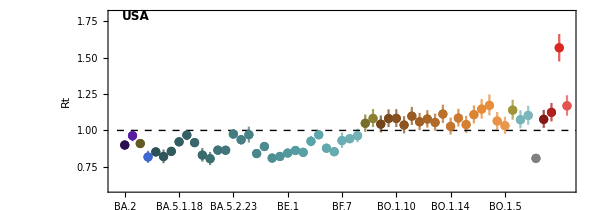

```mathematica
fig=Show[lines,points]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt-listplot.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt-listplot.png

```mathematica
topPos=Reverse[Ordering[finalRts,-8]];
```

```mathematica
tableValues=Table[{finalVariants[[p]],Round[finalRts[[p]],0.01],ToString[Round[finalRtsLower[[p]],0.01]]<>" - "<>ToString[Round[finalRtsUpper[[p]],0.01]]},{p,topPos}];
```

```mathematica
table=Style[TableForm[tableValues,TableHeadings->{None,{"lineage","Rt estimate","80% uncertainty interval"}},TableSpacing->{3,1}],FontFamily->"Helvetica",FontSize->12];
```

```mathematica
labels=Table[If[MemberQ[topPos,i],finalVariants[[i]],""],{i,Length[finalRts]}];
```

```mathematica
points=ListPlot[MapThread[{{#1,#2}}&,{finalFrequencies,finalRts}],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Current lineage frequency","Rt"},PlotStyle->Map[Directive[Opacity[0.75],#]&,finalColors],AspectRatio->0.65,ImageSize->350,PlotRange->{{0,0.23},{rtMin,rtMax}},FrameTicks->{{Automatic,Automatic},{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.05}],Automatic}},Epilog->{Text[Style["USA",Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{0,1},{n,1}}]},PlotLabels->Placed[labels,Right]];
```

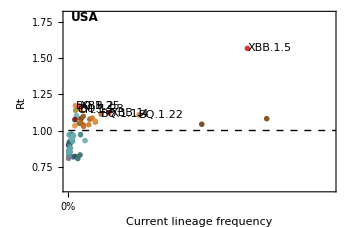
-Graphics- | lineage | Rt estimate | 80% uncertainty interval
XBB.1.5 | 1.57 | 1.47 - 1.66
BQ.1.25 | 1.17 | 1.1 - 1.25
XBB.2 | 1.17 | 1.1 - 1.24
BQ.1.23 | 1.15 | 1.08 - 1.22
CH.1.1 | 1.14 | 1.07 - 1.21
XBB.1 | 1.12 | 1.06 - 1.19
BQ.1.1.4 | 1.11 | 1.05 - 1.18
BQ.1.22 | 1.11 | 1.05 - 1.17

```mathematica
fig=Grid[{{points,table}}]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt-top.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt-top.png